```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Wed 7 Feb 2018 16:03:47

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.1.0 (December 27, 2017)

## At Day 12

[1] C. Arangala, Exploring Linear Algebra: Labs and Projects with Mathematica ®, 1st ed. Boca Raton: Chapman and Hall/CRC, 2014.

-Graphics-

## 1 Matrix Operation

## Lab 0: An Introduction to Mathematica^®

```mathematica
({{□, □}, {□, □}});
```

```mathematica
({{({{1, 1}, {1, 1}}), 0}, {0, 0}})//ArrayFlatten
```

{{1,1,0},{1,1,0},{0,0,0}}

## Lab 1: Matrix Basics and Operations

### Introduction

A matrix is a rectangular array of numbers. The numbers in the array is called the entries of the matrix. The general form of matrix is (a_11 | a_12 | a_13 | … | a_(1n)
a_21 | a_22 | a23 | … | a_(2n)
a_31 | a_32 | a_33 | … | a_(3n)
⋮ | ⋮ | ⋮ | ⋱ | ⋮
a_n1 | a_n2 | a_n3 | … | a_nn).

### Defining a Matrix in Mathematica

```mathematica
A=={{1,2,3},{4,5,6}}
SCMAF[%,MatrixForm,At[2]]
```

A=={{1,2,3},{4,5,6}}

A==(1 | 2 | 3
4 | 5 | 6)

```mathematica
A=={{1,2,3},{4,5,6}}
SCMAF[%,MatrixForm,At[2]]
```

A=={{1,2,3},{4,5,6}}

A==(1 | 2 | 3
4 | 5 | 6)

```mathematica
A==({{1, 2, 3}, {4, 5, 6}})
SCMAF[%,Dimensions,At[2],Take->{2}]
```

A̲=={{1,2,3},{4,5,6}}

{2,3}

### Operations on Matrices

#### Adding Two Matrices

```mathematica
SCARA[A+B,{A==({{1, 2, 3}, {4, 5, 6}}),B==({{3, 4}, {6, 7}, {9, 10}})},Apply->MatrixForm]
```

Thread::tdlen: Objects of unequal length in {{1,2,3},{4,5,6}}+{{3,4},{6,7},{9,10}} cannot be combined.

SCMAF::stopped: Stopped due to error.

A+B=={{1,2,3},{4,5,6}}+{{3,4},{6,7},{9,10}}

```mathematica
SCARA[A+M,{A==({{1, 2, 3}, {4, 5, 6}}),M==({{4, 5, 1}, {-1, 3, 2}})},Apply->MatrixForm]
```

A̲+M̲==(5 | 7 | 4
3 | 8 | 8)

```mathematica
SCARA[A+B,{A==({{1, 2, 3}, {4, 5, 6}})},Apply->MatrixForm]
```

A̲+B̲==(1+B̲ | 2+B̲ | 3+B̲
4+B̲ | 5+B̲ | 6+B̲)

#### Scalar Multiplication

```mathematica
SCARA[A+4,{A==({{1, 2, 3}, {4, 5, 6}})},Apply->MatrixForm]
```

4+A==(5 | 6 | 7
8 | 9 | 10)

```mathematica
SCARA[A+4,{A==({{1, 2}, {3, 4}})},Apply->MatrixForm,$,IdentityMatrix->False]
```

4+A==(5 | 2
3 | 8)

#### Multiplying Two Matrices

Demonstration: Matrix Multiplication

```mathematica
SCARA[A.B,{A==({{1, 2, 3}, {4, 5, 6}}),B==({{3, 4}, {6, 7}, {9, 10}})},Apply->MatrixForm]
```

A.B==(42 | 48
96 | 111)

#### The Transpose and Trace of a Matrix

a.

```mathematica
SCARA[A^T,A==({{1, 2, 3}, {4, 5, 6}}),MatrixForm->True]
```

A^T==(1 | 4
2 | 5
3 | 6)

b.

```mathematica
SCARA[HoldForm@Dimensions[Aᵀ],A==({{1, 2, 3}, {4, 5, 6}}),Apply->ReleaseHold]
```

Dimensions[A^T]=={3,2}

c.

```mathematica
SCAFE[(A^T)^T,Expand,All]
```

(A^T)^T==A

d.

```mathematica
SCAFE[(A+M)^T,Expand,All]
```

(A+M)^T==A^T+M^T

e.

```mathematica
SCAFE[(A.B)^T,Expand,{All}]
```

(A.B)^T==B^T.A^T

f.

```mathematica
SCARA[Transpose[A.B],{A==({{1, 2, 3}, {4, 5, 6}}),B==({{3, 4}, {6, 7}, {9, 10}})},MatrixForm->True]
```

(A.B)^T==(42 | 96
48 | 111)

```mathematica
SCARA[(B^T).A^T,{A==({{1, 2, 3}, {4, 5, 6}}),B==({{3, 4}, {6, 7}, {9, 10}})},MatrixForm->True]
```

B^T.A^T==(42 | 96
48 | 111)

g.

```mathematica
SCAFE[(3A)ᵀ,Expand,All]
```

True

```mathematica
SCAFE[HoldForm@(3 A̲)ᵀ,ReleaseHold,All]
```

(3 A̲)^T==3 (A̲)^T

h.

Exercises:

a.

```mathematica
SCARA[{Tr[U],Tr[V]},{U==({{1, 2, 3}, {4, 5, 0}, {0, 2, -1}}),V==({{1, 0, 0}, {4, 3, 0}, {0, 0, 2}})}]//Thread
```

{Tr[U]==5,Tr[V]==6}

b.

```mathematica
SCAFE[Tr[U+V],SCExpandFunc]
```

Tr[U+V]==Tr[U]+Tr[V]

c.

Some identities should be applied manually.

```mathematica
SCARA[{Tr[U],Tr[U^T]},U==({{1, 2, 3}, {4, 5, 0}, {0, 2, -1}})]//Thread
```

{Tr[U]==5,Tr[U^T]==5}

d.

```mathematica
SCARA[{Tr[U.V],Tr[U]Tr[V]},{U==({{1, 2, 3}, {4, 5, 0}, {0, 2, -1}}),V==({{1, 0, 0}, {4, 3, 0}, {0, 0, 2}})}]//Thread
```

{Tr[U.V]==22,Tr[U] Tr[V]==30}

e.

```mathematica
SCARA[{Tr[U.V],Tr[V.U]},{U==({{1, 2, 3}, {4, 5, 0}, {0, 2, -1}}),V==({{1, 0, 0}, {4, 3, 0}, {0, 0, 2}})}]//Thread
```

{Tr[U.V]==22,Tr[V.U]==22}

## Lab 2: A Matrix Representation of Linear Systems

### Introduction

A linear system,

```mathematica
Thread[Plus@@@Table[Subscript[a, i,j] Subscript[x, j],{i,4},{j,4}]==Table[Subscript[b, i],{i,4}]]//Column
```

x_1 a_(1,1)+x_2 a_(1,2)+x_3 a_(1,3)+x_4 a_(1,4)==b_1
x_1 a_(2,1)+x_2 a_(2,2)+x_3 a_(2,3)+x_4 a_(2,4)==b_2
x_1 a_(3,1)+x_2 a_(3,2)+x_3 a_(3,3)+x_4 a_(3,4)==b_3
x_1 a_(4,1)+x_2 a_(4,2)+x_3 a_(4,3)+x_4 a_(4,4)==b_4

can be written as a matrix equation

```mathematica
Thread[Plus@@@Table[Subscript[a, i,j] Subscript[x, j],{i,4},{j,4}]==Table[Subscript[b, i],{i,4}]]
SCMAF[%,CoefficientArrays,{All,Table[Subscript[x, i],{i,4}]},Apply->Normal,
MatrixForm@MatrixForm@#[[2]]·MatrixForm@Table[{Subscript[x, i]},{i,4}]==Transpose@{-#[[1]]}&,All]
```

{x_1 a_(1,1)+x_2 a_(1,2)+x_3 a_(1,3)+x_4 a_(1,4)==b_1,x_1 a_(2,1)+x_2 a_(2,2)+x_3 a_(2,3)+x_4 a_(2,4)==b_2,x_1 a_(3,1)+x_2 a_(3,2)+x_3 a_(3,3)+x_4 a_(3,4)==b_3,x_1 a_(4,1)+x_2 a_(4,2)+x_3 a_(4,3)+x_4 a_(4,4)==b_4}

{{-b_1,-b_2,-b_3,-b_4},{{a_(1,1),a_(1,2),a_(1,3),a_(1,4)},{a_(2,1),a_(2,2),a_(2,3),a_(2,4)},{a_(3,1),a_(3,2),a_(3,3),a_(3,4)},{a_(4,1),a_(4,2),a_(4,3),a_(4,4)}}}

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4))·(x_1
x_2
x_3
x_4)==(b_1
b_2
b_3
b_4)

```mathematica
Thread[Plus@@@Table[Subscript[a, i,j] Subscript[x, j],{i,4},{j,4}]==Table[Subscript[b, i],{i,4}]]
SCMAF[%,SCEqsMatForm,{All,Table[Subscript[x, i],{i,4}]}]
```

{x_1 a_(1,1)+x_2 a_(1,2)+x_3 a_(1,3)+x_4 a_(1,4)==b_1,x_1 a_(2,1)+x_2 a_(2,2)+x_3 a_(2,3)+x_4 a_(2,4)==b_2,x_1 a_(3,1)+x_2 a_(3,2)+x_3 a_(3,3)+x_4 a_(3,4)==b_3,x_1 a_(4,1)+x_2 a_(4,2)+x_3 a_(4,3)+x_4 a_(4,4)==b_4}

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4))·(x_1
x_2
x_3
x_4)==(b_1
b_2
b_3
b_4)

### The Identity Matrix

```mathematica
Subscript[Ι, n]==IdentityMatrix[n]
SCMAF[%,RA,{All,n==3},MatrixForm->True]
```

Ι_n==IdentityMatrix[n]

Ι_3==(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

### Row Echelon Form of a Matrix

A matrix is in row echelon form(ref) if
1) The first non-zero entry in each row is a one, called a leading one
2) Rows of all zeros are at the bottom of the matrix
3) All entries below leading ones are zeros
4) If i<j, the leading one in row i is to the left of the leading one in row j.

The matrix is in reduced row echelon form(rref) if
5) each column with a leading one has only zeros everywhere else.

Exercises:

a.

```mathematica
Subscript[Ι, 4]==MatrixForm@IdentityMatrix[4]
```

Ι_4==(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

b.

```mathematica
{2x+5y==7,4x+2y==10}
SCMAF[%,CoefficientArrays,{All,{x,y}},Apply->Normal,Part->2,
MatrixForm,All]
```

{2 x+5 y==7,4 x+2 y==10}

{{2,5},{4,2}}

(2 | 5
4 | 2)

c.

```mathematica
A==({{2, 5}, {4, 2}})
SCMAF[%,RowReduce,At[2],MatrixForm->True]
```

A=={{2,5},{4,2}}

A==(1 | 0
0 | 1)

### Elementary Row Operations and the Corresponding Elementary Matrices

#### 1. Swap two rows in a matrix.

```mathematica
Subscript[Ι, 2]
SCMAF[%,RA,{All,Subscript[Ι, 2]==IdentityMatrix[2]},MatrixForm->True,
SCSwapRows,{All,{1,2}}]
```

Ι_2

(1 | 0
0 | 1)

(0 | 1
1 | 0)

```mathematica
SCARA[Subscript[Ε, 1].Subscript[Ι, 2],{Subscript[Ι, 2]==IdentityMatrix[2],Subscript[Ε, 1]==({{0, 1}, {1, 0}})},MatrixForm->True]
```

Ε_1.Ι_2==(0 | 1
1 | 0)

#### 2. Multiply a row by a nonzero scalar (constant), k_1.

```mathematica
Subscript[Ι, 2]
SCMAF[%,RA,{All,Subscript[Ι, 2]==IdentityMatrix[2]},MatrixForm->True,
SCMultRow,{All,-1/8,2}]
```

Ι_2

(1 | 0
0 | 1)

(1 | 0
0 | -1/8)

```mathematica
SCARA[Subscript[Ε, 2].Subscript[Ι, 2],{Subscript[Ι, 2]==IdentityMatrix[2],Subscript[Ε, 2]==({{1, 0}, {0, -1/8}})},MatrixForm->True]
```

Ε_2.Ι_2==(1 | 0
0 | -1/8)

#### 3. Add a nonzero multiple k_2 of a row to another row.

```mathematica
Subscript[Ι, 2]
SCMAF[%,RA,{All,Subscript[Ι, 2]==IdentityMatrix[2]},MatrixForm->True,
SCRowsApply,{All,#1-2#2&,{2,1}}]
```

Ι_2

(1 | 0
0 | 1)

(1 | 0
-2 | 1)

```mathematica
SCARA[Subscript[Ε, 3].Subscript[Ι, 2],{Subscript[Ι, 2]==IdentityMatrix[2],Subscript[Ε, 3]==({{1, 0}, {-2, 1}})},MatrixForm->True]
```

Ε_3.Ι_2==(1 | 0
-2 | 1)

Exercises:

a.

```mathematica
SCARA[Subscript[Ε, 1].A,{Subscript[Ε, 1]==({{0, 1}, {1, 0}}),A==({{2, 5}, {4, 2}})},MatrixForm->True]
```

Ε_1.A==(4 | 2
2 | 5)

b.

```mathematica
SCARA[Subscript[Ε, 2].A,{Subscript[Ε, 2]==({{1, 0}, {0, -1/8}}),A==({{2, 5}, {4, 2}})},MatrixForm->True]
```

Ε_2.A==(2 | 5
-1/2 | -1/4)

c.

```mathematica
SCARA[Subscript[Ε, 3].A,{Subscript[Ε, 3]==({{1, 0}, {-2, 1}}),A==({{2, 5}, {4, 2}})},MatrixForm->True]
```

Ε_3.A==(2 | 5
0 | -8)

d.

```mathematica
SCARA[Subscript[Ε, 6].Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 2].Subscript[Ε, 3].A,{Subscript[Ε, 2]==({{1, 0}, {0, -1/8}}),Subscript[Ε, 3]==({{1, 0}, {-2, 1}}),Subscript[Ε, 4]==({{1/2, 0}, {0, 1}}),Subscript[Ε, 5]==({{1, -5}, {0, 1}}),Subscript[Ε, 6]==({{1, 5/2}, {0, 1}}),A==({{2, 5}, {4, 2}})},MatrixForm->True]
```

Ε_6.Ε_5.Ε_4.Ε_2.Ε_3.A==(1 | 0
0 | 1)

e.

```mathematica
SCARA[Subscript[Ε, 6].Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 2].Subscript[Ε, 3].b,{Subscript[Ε, 2]==({{1, 0}, {0, -1/8}}),Subscript[Ε, 3]==({{1, 0}, {-2, 1}}),Subscript[Ε, 4]==({{1/2, 0}, {0, 1}}),Subscript[Ε, 5]==({{1, -5}, {0, 1}}),Subscript[Ε, 6]==({{1, 5/2}, {0, 1}}),b==({{7}, {10}})},MatrixForm->True]
```

Ε_6.Ε_5.Ε_4.Ε_2.Ε_3.b==(9/4
1/2)

```mathematica
A.x==b
SCMAF[%,Subscript[Ε, 6].Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 2].Subscript[Ε, 3].#&,All,Level->1,
RA,{At[1],{Subscript[Ε, 6].Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 2].Subscript[Ε, 3].A==Ι}},
SCRemOp,{At[1],Ι}]
```

A.x==b

Ι.x==Ε_6.Ε_5.Ε_4.Ε_2.Ε_3.b

x==Ε_6.Ε_5.Ε_4.Ε_2.Ε_3.b

f.

```mathematica
{2x+5y==7,4x+2y==10}
SCMAF[%,CoefficientArrays,{All,{x,y}},Apply->Normal]
```

{2 x+5 y==7,4 x+2 y==10}

{{-7,-10},{{2,5},{4,2}}}

```mathematica
{2x+5y==7,4x+2y==10}
SCMAF[%,SCEqsMatForm,{All,{x,y}},Apply->Normal]
```

{2 x+5 y==7,4 x+2 y==10}

(2 | 5
4 | 2)·(x
y)==(7
10)

Solve the system of equations.

```mathematica
({{2, 5}, {4, 2}})//MatrixForm
SCMAF[%,SCAppendColumn,{All,({{7}, {10}})},
SCMultRow,{All,1/2,1},MatrixForm->True,
SCRowsApply,{All,#1-4#2&,{2,1}},
SCMultRow,{All,-1/8,2},
SCRowsApply,{All,#1-5/2#2&,{1,2}}]
```

(2 | 5
4 | 2)

(1 | 5/2 | 7/2
0 | 1 | 1/2)

(1 | 0 | 9/4
0 | 1 | 1/2)

```mathematica
({{x}, {y}})==LinearSolve[({{2, 5}, {4, 2}}),({{7}, {10}})]
SCMAF[%,MatrixForm,All,Level->{1}]
```

{{x},{y}}=={{9/4},{1/2}}

(x
y)==(9/4
1/2)

g.

```mathematica
M==({{1, 2, 0}, {0, 0, 3}, {0, 1, 0}})
SCMAF[%,Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1].#&,All,Level->{1},
RA,{At[2],{Subscript[Ε, 1]==({{1, 0, -2}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0}, {0, 1/3, 0}, {0, 0, 1}}),Subscript[Ε, 3]==({{1, 0, 0}, {0, 0, 1}, {0, 1, 0}})}},MatrixForm->True]
```

M=={{1,2,0},{0,0,3},{0,1,0}}

Ε_3.Ε_2.Ε_1.M==Ε_3.Ε_2.Ε_1.{{1,2,0},{0,0,3},{0,1,0}}

Ε_3.Ε_2.Ε_1.M==(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
SCARA[Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1],{Subscript[Ε, 1]==({{1, 0, -2}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0}, {0, 1/3, 0}, {0, 0, 1}}),Subscript[Ε, 3]==({{1, 0, 0}, {0, 0, 1}, {0, 1, 0}})},MatrixForm->True]
```

Ε_3.Ε_2.Ε_1==(1 | 0 | -2
0 | 0 | 1
0 | 1/3 | 0)

h.

```mathematica
({{x}, {y}, {z}})==Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1].({{4}, {6}, {8}})
SCMAF[%,RA,{At[2],{Subscript[Ε, 1]==({{1, 0, -2}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0}, {0, 1/3, 0}, {0, 0, 1}}),Subscript[Ε, 3]==({{1, 0, 0}, {0, 0, 1}, {0, 1, 0}})}},MatrixForm->True]
```

{{x},{y},{z}}==Ε_3.Ε_2.Ε_1.{{4},{6},{8}}

(x
y
z)==(-12
8
2)

i, j.

```mathematica
{x+2y==4,y+3z==6,2y+6z==18}
SCMAF[%,CoefficientArrays,{All,{x,y,z}},Apply->Normal]
```

{x+2 y==4,y+3 z==6,2 y+6 z==18}

{{-4,-6,-18},{{1,2,0},{0,1,3},{0,2,6}}}

```mathematica
SCARA[Subscript[Ε, 2].Subscript[Ε, 1].A,{A=={{1,2,0},{0,1,3},{0,2,6}},Subscript[Ε, 1]==({{1, 0, 0}, {0, 1, 0}, {0, -2, 1}}),Subscript[Ε, 2]==({{1, -2, 0}, {0, 1, 0}, {0, 0, 1}})},MatrixForm->True]
```

Ε_2.Ε_1.A==(1 | 0 | -6
0 | 1 | 3
0 | 0 | 0)

```mathematica
({{x}, {y}, {z}})==LinearSolve[{{1,2,0},{0,1,3},{0,2,6}},-{-4,-6,-18}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

{{x},{y},{z}}==LinearSolve[{{1,2,0},{0,1,3},{0,2,6}},{4,6,18}]

## Lab 3: Powers, Inverses, and Special Matrices

### Introduction

A square matrix is a n×n matrix. If A.B=B.A=I, then A is said to be invertible or nonsingular and B is called the inverse of A. If there is no such matrix B, then A is said to be singular.

### Powers of matrices

Exercises:

a.

```mathematica
SCARA[A^2,{A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}})},MatrixForm->True]
```

A^2==(1 | 4 | 0
4 | 1 | 0
0 | 1 | 4)

```mathematica
SCARR[A^2,{A_^n_:>Dot[Sequence@@Table[A,n]],A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}})},MatrixForm->True]
```

A^2==(5 | 4 | 0
4 | 5 | 0
2 | -1 | 4)

```mathematica
SCARR[A^2,{A_^n_->MatrixPower[A,n],A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}})},MatrixForm->True]
```

A^2==(5 | 4 | 0
4 | 5 | 0
2 | -1 | 4)

b.

The matrix to be powered should be square.

```mathematica
SCARR[B^2,{A_^n_->MatrixPower[A,n],B==({{1, -1}, {9, 3}, {0, 4}})},MatrixForm->True]
```

MatrixPower::matsq: Argument {{1,-1},{9,3},{0,4}} at position 1 is not a non-empty square matrix.

SCMAF::stopped: Stopped due to error.

B^2==MatrixPower[(1 | -1
9 | 3
0 | 4),2]

c.

```mathematica
SCARR[A^0,{A_^n_->MatrixPower[A,n],A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}})},MatrixForm->True]
```

A^0==(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

d.

```mathematica
SCAFE[(A^r).A^s,SCOpExpand,All]
```

A^r.A^s==A^(r+s)

```mathematica
SCAFE[(A^r)^s,PowerExpand,All]
```

(A^r)^s==A^(r s)

### Inverse of a Matrix

Exercises:

a.

Inverse[A] returns the inverse matrix of A.

```mathematica
A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}})
SCMAF[%,Inverse,All,Level->{1},MatrixForm->True]
```

A=={{1,2,0},{2,1,0},{0,1,-2}}

A^-1==(-1/3 | 2/3 | 0
2/3 | -1/3 | 0
1/3 | -1/6 | -1/2)

```mathematica
SCARA[A.A^-1,A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}}),MatrixForm->True]
```

A.A^-1==(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
SCARA[(A^-1).A,A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}}),MatrixForm->True]
```

A^-1.A==(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

b.

```mathematica
SCAFE[((A̲)^-1)^-1,Simplify]
```

((A̲)^-1)^-1==A̲

```mathematica
SCARA[(A^-1)^-1,A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}}),MatrixForm->True]
```

(A^-1)^-1==(1 | 2 | 0
2 | 1 | 0
0 | 1 | -2)

c.

```mathematica
SCARA[{(A.M)^-1,(M.A)^-1,(A^-1).M^-1,(M^-1).A^-1},{A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}}),M==({{1, 2, 3}, {0, 5, 6}, {7, 8, 9}})},MatrixForm->True]//Thread
```

{(A.M)^-1==(-1/6 | 7/48 | -1/16
1 | -11/8 | -1/8
-13/18 | 157/144 | 5/48),(M.A)^-1==(-29/24 | 5/12 | 1/8
2/3 | -1/3 | 0
-19/48 | -1/24 | 5/48),A^-1.M^-1==(-29/24 | 5/12 | 1/8
2/3 | -1/3 | 0
-19/48 | -1/24 | 5/48),M^-1.A^-1==(-1/6 | 7/48 | -1/16
1 | -11/8 | -1/8
-13/18 | 157/144 | 5/48)}

d.

```mathematica
SCARA[(A^T)^-1,A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}}),MatrixForm->True]
```

(A^T)^-1==(-1/3 | 2/3 | 1/3
2/3 | -1/3 | -1/6
0 | 0 | -1/2)

```mathematica
SCARA[(A^-1)^T,A==({{1, 2, 0}, {2, 1, 0}, {0, 1, -2}}),MatrixForm->True]
```

(A^-1)^T==(-1/3 | 2/3 | 1/3
2/3 | -1/3 | -1/6
0 | 0 | -1/2)

```mathematica
SCAFE[{((A̲.M̲)^T)^-1,((M̲.A̲)^T)^-1},SCOpExpand,{All,Vectors->_UnderBar}]//Thread
SCMAF[%,RA,{At[All,2],(A_ .B_)^-1->(B^-1).A^-1}(*A, B may not be square matrices.*)]
```

{((A̲.M̲)^T)^-1==((M̲)^T.(A̲)^T)^-1,((M̲.A̲)^T)^-1==((A̲)^T.(M̲)^T)^-1}

{((A̲.M̲)^T)^-1==((A̲)^T)^-1.((M̲)^T)^-1,((M̲.A̲)^T)^-1==((M̲)^T)^-1.((A̲)^T)^-1}

e.

```mathematica
SCARA[P^-1,P==({{1, 4, 0}, {2, 5, 0}, {3, 6, 0}})]
```

Inverse::sing: Matrix {{1,4,0},{2,5,0},{3,6,0}} is singular.

SCMAF::stopped: Stopped due to error.

P^-1=={{1,4,0},{2,5,0},{3,6,0}}^-1

### Special Matrices

A is symmetric if A=A^T.

A is diagonal if A_(i,j)=0 if i≠j.

A is upper triangular if A_(i,j)=0 when i>j and is lower triangular if A_(i,j)=0 when i<j.

Exercises:

a.

```mathematica
SCAFE[(A+A^T)^T,Expand]
```

(A+A^T)^T==A+A^T

A+A^T is a symmetric matrix.

b.

```mathematica
SCARA[Q^T,Q==({{1, 0}, {2, 3}}),MatrixForm->True]
```

Q^T==(1 | 2
0 | 3)

If Q is lower triangular, then Q^T is upper triangular.

c.

```mathematica
Table[Q^n==MatrixPower[Q,n],{n,3}]
SCMAF[%,RA,{At[All,2],Q==({{1, 0}, {2, 3}})},MatrixForm->True]
```

{Q==MatrixPower[Q,1],Q^2==MatrixPower[Q,2],Q^3==MatrixPower[Q,3]}

{Q==(1 | 0
2 | 3),Q^2==(1 | 0
8 | 9),Q^3==(1 | 0
26 | 27)}

### Theorem and Problems

Theorem 1. The inverse of an elementary matrix is an elementary matrix.

Theorem 2. If A is invertible then the reduced row echelon form of A is I.

Theorem 3. If the reduced row echelon form of A is I then A is invertible.

Theorem 4. A is a square invertible matrix iff A can be written as the product of elementary matrices.

Problem 5. If A is invertible then A^k is invertible for any integer k.

Problem 6. If A and B are square matrices of the same size then A and B are invertible iff A.B is invertible.

## Lab 4: Graph Theory and Adjacent Matrices

### Basics of Graph Theory

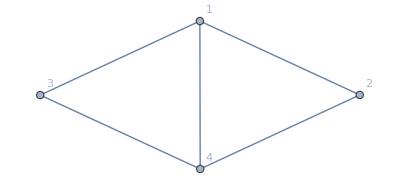

```mathematica
Graph[{1<->2,1<->3,1<->4,2<->4,3<->4},VertexLabels->"Name"]
```

a, b.

```mathematica
{1<->2,1<->3,1<->4,2<->4,3<->4}//AdjacencyMatrix//MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0)

c.

```mathematica
AdjacencyGraph[({{0, 1, 1, 1}, {1, 0, 0, 1}, {1, 0, 0, 1}, {1, 1, 1, 0}}),VertexLabels->"Name"]
```

-Graphics-

d, e.

There are two 2-step paths between vertex 1 and 4. A^2 shows the number of 2-step paths between vertices.

```mathematica
SCARA[A^2,A_^n_->MatrixPower[A,n]]
SCMAF[%,RA,{At[2],A==Normal@({{0, 1, 1, 1}, {1, 0, 0, 1}, {1, 0, 0, 1}, {1, 1, 1, 0}})},MatrixForm->True]
```

A^2==MatrixPower[A,2]

A^2==(3 | 1 | 1 | 2
1 | 2 | 2 | 1
1 | 2 | 2 | 1
2 | 1 | 1 | 3)

f.

A^3 shows the number of 3-step paths between vertices.

```mathematica
SCARA[A^3,A_^n_->MatrixPower[A,n]]
SCMAF[%,RA,{At[2],A==Normal@({{0, 1, 1, 1}, {1, 0, 0, 1}, {1, 0, 0, 1}, {1, 1, 1, 0}})},MatrixForm->True]
```

A^3==MatrixPower[A,3]

A^3==(4 | 5 | 5 | 5
5 | 2 | 2 | 5
5 | 2 | 2 | 5
5 | 5 | 5 | 4)

### An Application to Hospital Placements in Ghana

Find minimum number of national hospitals and their locations to cover all 14 largest cities in Ghana.

```mathematica
GeoGraphics@Entity["Country","Ghana"]
```

-Graphics-

```mathematica
GeoListPlot[,GeoLabels->True,GeoRange->Entity["Country","Ghana"]]
cityList=EntityList@;
```

-Graphics-

Connect 5 nearest cities from each city.

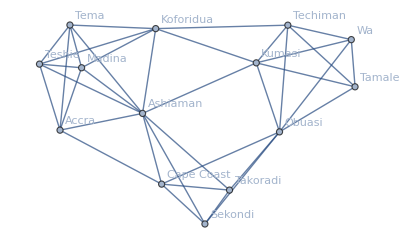

```mathematica
SimpleGraph[Flatten[Table[{#[[1]]<->#[[n]]},{n,2,5}]&/@(GeoNearest[cityList,#,5]&/@cityList)],VertexLabels->"Name"]
```

Remove too short or too long paths.

```mathematica
graphPool=DeleteDuplicates[Flatten[Table[{#[[1]]<->#[[n]]},{n,2,5}]&/@(GeoNearest[cityList,#,5]&/@cityList)],#1==Reverse@#2&]
```

{Accra<->Teshie,Accra<->Madina,Accra<->Ashiaman,Accra<->Tema,Kumasi<->Obuasi,Kumasi<->Techiman,Kumasi<->Koforidua,Kumasi<->Ashiaman,Tamale<->Wa,Tamale<->Techiman,Tamale<->Kumasi,Tamale<->Obuasi,Ashiaman<->Madina,Ashiaman<->Teshie,Ashiaman<->Tema,Takoradi<->Sekondi,Takoradi<->Cape Coast,Takoradi<->Obuasi,Takoradi<->Ashiaman,Obuasi<->Cape Coast,Obuasi<->Sekondi,Teshie<->Madina,Teshie<->Tema,Cape Coast<->Sekondi,Cape Coast<->Ashiaman,Cape Coast<->Accra,Tema<->Madina,Sekondi<->Ashiaman,Koforidua<->Ashiaman,Koforidua<->Madina,Koforidua<->Tema,Koforidua<->Teshie,Techiman<->Obuasi,Techiman<->Koforidua,Wa<->Techiman,Wa<->Kumasi,Wa<->Obuasi}

```mathematica
QuantityMagnitude@TravelDistance[#[[1]],#[[2]]]&/@graphPool
```

{13.378,14.8359,25.0294,33.4887,66.9714,120.11,190.386,237.82,301.976,258.058,377.251,442.601,27.2129,35.9347,48.5815,9.01152,81.041,209.501,229.504,169.232,200.165,22.3934,15.8337,71.706,149.404,141.254,32.0345,220.178,64.8839,63.3004,84.6196,85.0252,185.421,300.219,322.095,441.662,507.012}

{Kumasi<->Obuasi,Kumasi<->Techiman,Kumasi<->Koforidua,Kumasi<->Ashiaman,Tamale<->Wa,Tamale<->Techiman,Takoradi<->Cape Coast,Takoradi<->Obuasi,Takoradi<->Ashiaman,Obuasi<->Cape Coast,Obuasi<->Sekondi,Cape Coast<->Sekondi,Cape Coast<->Ashiaman,Cape Coast<->Accra,Sekondi<->Ashiaman,Koforidua<->Ashiaman,Koforidua<->Madina,Koforidua<->Tema,Koforidua<->Teshie,Techiman<->Obuasi,Techiman<->Koforidua,Wa<->Techiman}

{22,14}

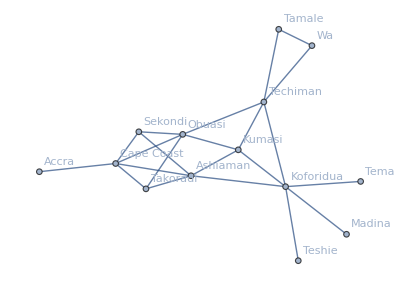

```mathematica
graph=Select[graphPool,50<QuantityMagnitude@TravelDistance[#[[1]],#[[2]]]<350&]
{EdgeCount[%],VertexCount[%]}
Graph[%%,VertexLabels->"Name"]
```

```mathematica
Show[
GeoGraphics[(GeoPath@{#1,#2}&)@@@graph,GeoRange->Entity["Country","Ghana"]],
GeoListPlot[,GeoLabels->True]]
```

-Graphics-

Find maximum 2-cities path.

```mathematica
VertexList[graph]
SCARA[A+A.A,{A==Normal@AdjacencyMatrix[graph]},MatrixForm->True]
```

{Kumasi,Obuasi,Techiman,Koforidua,Ashiaman,Tamale,Wa,Takoradi,Cape Coast,Sekondi,Accra,Madina,Tema,Teshie}

A+A.A==(4 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 2 | 2 | 0 | 1 | 1 | 1
2 | 5 | 2 | 2 | 4 | 1 | 1 | 2 | 3 | 2 | 1 | 0 | 0 | 0
3 | 2 | 5 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 1
3 | 2 | 2 | 6 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
2 | 4 | 2 | 2 | 5 | 0 | 0 | 2 | 3 | 2 | 1 | 1 | 1 | 1
1 | 1 | 2 | 1 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 1 | 1 | 2 | 0 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 0
2 | 3 | 1 | 1 | 3 | 0 | 0 | 3 | 5 | 3 | 1 | 0 | 0 | 0
2 | 2 | 1 | 1 | 2 | 0 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1)

At least two national hospitals are required to cover 14 largest cities.

```mathematica
cityList=.
graph=.
graphPool=.
```

## Lab 5: Permutations and Determinants

### Permutations

Demonstration: Permutation Notations

There are n! permutations for a n sequence.

Demonstration: Signed Determinant Terms

Demonstration: 3×3 Determinants Using Diagonals

### Determinants

Exercises:

a.

```mathematica
SCARA[{Det[A],Det[A^-1]},A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}})]//Thread
SCMAF[%,SCMultEqs,All]
```

{Det[A]==4,Det[A^-1]==1/4}

Det[A] Det[A^-1]==1

b.

```mathematica
SCARA[Det[B],B==({{2, 4}, {4, 8}})]
```

Det[B]==0

B is not invertible.

c.

```mathematica
SCARA[{Det[Subscript[Ι, 2]],Det[Subscript[Ι, 4]]},Subscript[Ι, n_]==IdentityMatrix[4]]//Thread
```

{Det[Ι_2]==1,Det[Ι_4]==1}

We can infer that det[Ι_n]=1.

d.

```mathematica
SCARA[{Det[A],Det[A^T]},A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}})]//Thread
SCMAF[%,Reverse,At[2],
SCMultEqs,All,Apply->Simplify]
```

{Det[A]==4,Det[A^T]==4}

{Det[A]==4,4==Det[A^T]}

Det[A]==Det[A^T]

e.

```mathematica
SCARA[{Det[A],Det[2A]},A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}})]//Thread
SCMAF[%,Reverse,At[2],
SCMultEqs,All,Apply->Simplify]
```

{Det[A]==4,Det[2 A]==32}

{Det[A]==4,32==Det[2 A]}

8 Det[A]==Det[2 A]

```mathematica
SCARA[{Det[A],Det[3A]},A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}})]//Thread
SCMAF[%,Reverse,At[2],
SCMultEqs,All,Apply->Simplify]
```

{Det[A]==4,Det[3 A]==108}

{Det[A]==4,108==Det[3 A]}

27 Det[A]==Det[3 A]

```mathematica
SCARA[{Det[P],Det[2P]},P==({{1, 4}, {2, 5}})]//Thread
SCMAF[%,Reverse,At[2],
SCMultEqs,All,Apply->Simplify]
```

{Det[P]==-3,Det[2 P]==-12}

{Det[P]==-3,-12==Det[2 P]}

4 Det[P]==Det[2 P]

```mathematica
SCARA[{Det[P],Det[3P]},P==({{1, 4}, {2, 5}})]//Thread
SCMAF[%,Reverse,At[2],
SCMultEqs,All,Apply->Simplify]
```

{Det[P]==-3,Det[3 P]==-27}

{Det[P]==-3,-27==Det[3 P]}

9 Det[P]==Det[3 P]

f.

```mathematica
SCARA[{Det[A.M],Det[M.A]},{A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}}),M==({{1, 2, 3}, {0, 5, 6}, {7, 8, 9}})}]//Thread
SCMAF[%,Reverse,At[2],
SCMultEqs,All,Apply->Simplify]
```

{Det[A.M]==-96,Det[M.A]==-96}

{Det[A.M]==-96,-96==Det[M.A]}

Det[A.M]==Det[M.A]

g.

```mathematica
SCARA[{Det[A+M],Det[M+A]},{A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}}),M==({{1, 2, 3}, {0, 5, 6}, {7, 8, 9}})}]//Thread
```

{Det[A+M]==4,Det[A+M]==4}

h.

```mathematica
SCARA[{Det[A+M],Det[M]+Det[A]},{A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}}),M==({{1, 2, 3}, {0, 5, 6}, {7, 8, 9}})}]//Thread
```

{Det[A+M]==4,Det[A]+Det[M]==-20}

i.

```mathematica
SCARA[{Det[V],Det[W]},{V==({{1, 0, 0}, {4, 3, 0}, {0, 0, 2}}),W==({{5, 0, 0}, {0, 4, 0}, {0, 0, -1}})}]//Thread
```

{Det[V]==6,Det[W]==-20}

j. Cayley-Hamilton Theorem

```mathematica
SCARR[{(Tr[P]^2-Tr[P^2])/2,Det[P]},{P^n_->MatrixPower[P,2],P==({{1, 4}, {2, 5}})}]//Thread
SCMAF[%,Reverse,At[1],
SCMultEqs,All,
SCDivEq,{All,-3}]
```

{1/2 (Tr[P]^2-Tr[P^2])==-3,Det[P]==-3}

-3 Det[P]==-3/2 (Tr[P]^2-Tr[P^2])

Det[P]==1/2 (Tr[P]^2-Tr[P^2])

```mathematica
SCARR[{(Tr[M]^3-3Tr[M^2]Tr[M]+2Tr[M^3])/6,Det[M]},{M^n_->MatrixPower[M,n],M==({{1, 2, 3}, {0, 5, 6}, {7, 8, 9}})}]//Thread
SCMAF[%,Reverse,At[1],
SCMultEqs,All,
SCDivEq,{All,-24}]
```

{1/6 (Tr[M]^3-3 Tr[M] Tr[M^2]+2 Tr[M^3])==-24,Det[M]==-24}

-24 Det[M]==-4 (Tr[M]^3-3 Tr[M] Tr[M^2]+2 Tr[M^3])

Det[M]==1/6 (Tr[M]^3-3 Tr[M] Tr[M^2]+2 Tr[M^3])

### Determinants of Elementary Matrices as They Relate to Invertible Matrices

Exercises:

a.

If E results from multiplying a single row of Ι by a constant k, it follows that det(E)=k.

```mathematica
SCARA[Det[Subscript[Ε, 1]],Subscript[Ε, 1]==({{1/2, 0}, {0, 1}})]
```

Det[Ε_1]==1/2

b.

If E results from adding or subtracting a multiple of one row of I to another, then it follows that det(E)=1.

```mathematica
SCARA[Det[Subscript[Ε, 2]],Subscript[Ε, 2]==({{1, 0}, {-4, 1}})]
```

Det[Ε_2]==1

c.

If E results from interchanging two rows of I, then it follows that det(E)=−1.

```mathematica
SCARA[Det[Subscript[Ε, 3]],Subscript[Ε, 3]==({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})]
```

Det[Ε_3]==-1

### Theorems and Problems

Theorem 13. If det(A) is not 0 then A is invertible.

Theorem 14. If A is invertible then det(A) is not 0.

Theorem 15. If A and B are invertible matrices of the same size then A+B is invertible.

Theorem 16. If A is a square matrix then det(A)=det(A^T).

Theorem 17. A and B are invertible matrices iff A.B is invertible.

## Lab 6: 4×4 Determinants and Beyond

### Cofactor Expansion

det(A)=∑_(j=1)^n (-1)^(i+j)a_(i,j)M_(i,j)=∑_(i=1)^n (-1)^(i+j)a_(i,j)M_(i,j)

Exercises:

a.

```mathematica
{Subscript[M, 4,1],Subscript[M, 4,2],Subscript[M, 4,3],Subscript[M, 4,4]}/.Subscript[M, i_,j_]:>Det@Transpose@(ReplaceAll[#,#[[j]]->Nothing]&)@Transpose@(ReplaceAll[#,#[[i]]->Nothing]&)[({{1, 1, 0, 0}, {1, 2, 1, 0}, {2, 1, 3, 1}, {0, 0, 1, 4}})]
```

{1,1,1,4}

```mathematica
SCARA[{Subscript[M, 4,1],Subscript[M, 4,2],Subscript[M, 4,3],Subscript[M, 4,4]},Subscript[M, i_,j_]->Det@SCDelColumn[SCDelRow[({{1, 1, 0, 0}, {1, 2, 1, 0}, {2, 1, 3, 1}, {0, 0, 1, 4}}),i],j]]//Thread
```

{M_(4,1)==1,M_(4,2)==1,M_(4,3)==1,M_(4,4)==4}

b.

```mathematica
Det[A]==∑_(j=1)^n (-1)^(i+j)Subscript[a, i,j] Subscript[M, i,j]
SCMAF[%,RA,{At[2],{n==4,i==4}},Apply->SCEvalSum,
RA,{At[2],{Subscript[a, i_,j_]:>({{1, 1, 0, 0}, {1, 2, 1, 0}, {2, 1, 3, 1}, {0, 0, 1, 4}})[[i,j]]}},
RA,{At[2],{Subscript[M, 4,1]==1,Subscript[M, 4,2]==1,Subscript[M, 4,3]==1,Subscript[M, 4,4]==4}}]
```

Det[A]==∑_(j=1)^n (-1)^(i+j) a_(i,j) M_(i,j)

Det[A]==-M_(4,3)+4 M_(4,4)

Det[A]==15

```mathematica
SCARA[Det[A],A==({{1, 1, 0, 0}, {1, 2, 1, 0}, {2, 1, 3, 1}, {0, 0, 1, 4}})]
```

Det[A]==15

c.

```mathematica
Det[A]==∑_(i=1)^n (-1)^(i+j)Subscript[a, i,j] Subscript[M, i,j]
SCMAF[%,RA,{At[2],{n==4,j==4}},Apply->SCEvalSum,
RA,{At[2],Subscript[a, i_,j_]:>({{1, 1, 0, 0}, {1, 2, 1, 0}, {2, 1, 3, 1}, {0, 0, 1, 4}})[[i,j]]},
RA,{At[2],Subscript[M, i_,j_]->Det@SCDelColumn[SCDelRow[({{1, 1, 0, 0}, {1, 2, 1, 0}, {2, 1, 3, 1}, {0, 0, 1, 4}}),i],j]}]
```

Det[A]==∑_(i=1)^n (-1)^(i+j) a_(i,j) M_(i,j)

Det[A]==-M_(3,4)+4 M_(4,4)

Det[A]==15

d.

```mathematica
Det[B]==∑_(i=1)^n (-1)^(i+j)Subscript[b, i,j] Subscript[M, i,j]
SCMAF[%,RA,{At[2],{n==4,j==1}},Apply->SCEvalSum,
RA,{At[2],Subscript[b, i_,j_]:>({{1, 1, 0, 0}, {0, 1, 1, 0}, {0, -1, 3, 1}, {0, 0, 1, 4}})[[i,j]]},RA,{At[2],Subscript[M, i_,j_]->Det@SCDelColumn[SCDelRow[({{1, 1, 0, 0}, {0, 1, 1, 0}, {0, -1, 3, 1}, {0, 0, 1, 4}}),i],j]}]
```

Det[B]==∑_(i=1)^n (-1)^(i+j) b_(i,j) M_(i,j)

Det[B]==M_(1,1)

Det[B]==15

```mathematica
SCARA[Det[B],B==({{1, 1, 0, 0}, {0, 1, 1, 0}, {0, -1, 3, 1}, {0, 0, 1, 4}})]
```

Det[B]==15

```mathematica
Off[Part::partd]
Det[P]==Product[P_[[i,i]],{i,4}]
SCMAF[%,RA,{All,P==({{1, 1, 0, 0}, {0, 1, 1, 0}, {0, 0, 1, 4}, {0, 0, 0, -15}})}]
On[Part::partd]
```

Det[P]==P⟦1,1⟧ P⟦2,2⟧ P⟦3,3⟧ P⟦4,4⟧

True

e.

```mathematica
SCARA[Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1].B,{B==({{1, 1, 0, 0}, {0, 1, 1, 0}, {0, -1, 3, 1}, {0, 0, 1, 4}}),Subscript[Ε, 1]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 1, 1, 0}, {0, 0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1/4, 0}, {0, 0, 1, 4}}),Subscript[Ε, 3]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, -8, 1}}),Subscript[Ε, 4]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}),Subscript[Ε, 5]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, -1/4}, {0, 0, 0, 1}})},MatrixForm->True]
```

Ε_5.Ε_4.Ε_3.Ε_2.Ε_1.B==(1 | 1 | 0 | 0
0 | 1 | 1 | 0
0 | 0 | 1 | 4
0 | 0 | 0 | -15)

f.

```mathematica
SCARA[Table[Det[Subscript[Ε, n]],{n,5}],{Subscript[Ε, 1]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 1, 1, 0}, {0, 0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1/4, 0}, {0, 0, 1, 4}}),Subscript[Ε, 3]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, -8, 1}}),Subscript[Ε, 4]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}),Subscript[Ε, 5]==({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, -1/4}, {0, 0, 0, 1}})}]//Thread
```

{Det[Ε_1]==1,Det[Ε_2]==1,Det[Ε_3]==1,Det[Ε_4]==-1,Det[Ε_5]==1}

## 2 Invertibility

## Lab 7: Singular or Nonsingular? Why Singularity Matters

### Introduction

If A is an n×n matrix then the following are equivalent:

1. A is invertible.
2. |A|≠0.
3. The rref of A is Ι_n.

### Finding Inverses

Exercises:

```mathematica
A|Ι
SCMAF[%,RA,{All,{A==({{2, 2, 0}, {2, 1, 0}, {0, 1, -2}}),Ι==IdentityMatrix[3]}},
Subscript[Ε, 6].Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1].#&,All,Level->{1},
RA,{All,{Subscript[Ε, 1]==({{1/2, 0, 0}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0}, {-2, 1, 0}, {0, 0, 1}}),Subscript[Ε, 3]==({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}}),Subscript[Ε, 4]==({{1, -1, 0}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 5]==({{1, 0, 0}, {0, 1, 0}, {0, -1, 1}}),Subscript[Ε, 6]==({{1, 0, 0}, {0, 1, 0}, {0, 0, -1/2}})}},MatrixForm->True]
```

A|Ι

Ε_6.Ε_5.Ε_4.Ε_3.Ε_2.Ε_1.{{2,2,0},{2,1,0},{0,1,-2}}|Ε_6.Ε_5.Ε_4.Ε_3.Ε_2.Ε_1.{{1,0,0},{0,1,0},{0,0,1}}

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)|(-1/2 | 1 | 0
1 | -1 | 0
1/2 | -1/2 | -1/2)

d.

```mathematica
Subscript[Ε, 6].Subscript[Ε, 5].Subscript[Ε, 4].Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1].A==Ι
SCMAF[%,(Subscript[Ε, 1]^-1).(Subscript[Ε, 2]^-1).(Subscript[Ε, 3]^-1).(Subscript[Ε, 4]^-1).(Subscript[Ε, 5]^-1).(Subscript[Ε, 6]^-1).#&,All,Level->{1},
SCRemUnity,Table[{At[1]},6]]
```

Ε_6.Ε_5.Ε_4.Ε_3.Ε_2.Ε_1.A==Ι

Ε_1^-1.Ε_2^-1.Ε_3^-1.Ε_4^-1.Ε_5^-1.1.Ε_5.Ε_4.Ε_3.Ε_2.Ε_1.A==Ε_1^-1.Ε_2^-1.Ε_3^-1.Ε_4^-1.Ε_5^-1.Ε_6^-1.Ι

A==Ε_1^-1.Ε_2^-1.Ε_3^-1.Ε_4^-1.Ε_5^-1.Ε_6^-1.Ι

```mathematica
SCARA[Table[Subscript[Ε, n]^-1,{n,6}],{Subscript[Ε, 1]==({{1/2, 0, 0}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 2]==({{1, 0, 0}, {-2, 1, 0}, {0, 0, 1}}),Subscript[Ε, 3]==({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}}),Subscript[Ε, 4]==({{1, -1, 0}, {0, 1, 0}, {0, 0, 1}}),Subscript[Ε, 5]==({{1, 0, 0}, {0, 1, 0}, {0, -1, 1}}),Subscript[Ε, 6]==({{1, 0, 0}, {0, 1, 0}, {0, 0, -1/2}})},MatrixForm->True]//Thread
```

{Ε_1^-1==(2 | 0 | 0
0 | 1 | 0
0 | 0 | 1),Ε_2^-1==(1 | 0 | 0
2 | 1 | 0
0 | 0 | 1),Ε_3^-1==(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1),Ε_4^-1==(1 | 1 | 0
0 | 1 | 0
0 | 0 | 1),Ε_5^-1==(1 | 0 | 0
0 | 1 | 0
0 | 1 | 1),Ε_6^-1==(1 | 0 | 0
0 | 1 | 0
0 | 0 | -2)}

### Using Inverses to Solve Systems of Linear Equations

a.

```mathematica
A.x==b
SCMAF[%,(A^-1).#&,All,Level->{1},
SCRemOp,{At[1],1},
RA,{At[2],{A==({{1, 2, 0}, {0, 1, 3}, {1, 2, 6}}),b==({{7}, {10}, {0}})}},MatrixForm->True]
```

A.x==b

x==A^-1.b

x==(-20
27/2
-7/6)

b.

```mathematica
A.x==b
SCMAF[%,(A^-1).#&,All,Level->{1},
SCRemOp,{At[1],1},
RA,{At[2],{A==({{1, 2, 0}, {0, 1, 3}, {1, 2, 6}}),b==({{0}, {0}, {0}})}},MatrixForm->True]
```

A.x==b

x==A^-1.b

x==(0
0
0)

### Theorems and Problems

Problem 18. The inverse of a nonsingular upper triangular matrix is upper triangular.

Problem 19. The inverse of a nonsingular diagonal matrix is diagonal.

Problem 20. |A^-1|=1/(|A|).

Theorem 21. A is invertible iff A can be written as a product of elementary matrices.

Theorem 22. If A is an n×n invertible matrix then the system A.x=b has exactly one solution for all n×1 vectors b.

Theorem 23. If A is an n×n matrix and the system A.x=b is consistent (has at least one solution) for all n×1 vectors b then A is invertible.

Problem 24. If a d-b c≠0  then (a | b
c | d )^-1=1/(a d-b c)(d | -b
-c | a).

True.

```mathematica
SCAFE[HoldForm@Inverse[MatrixForm@({{a, b}, {c, d}})],ReleaseHold,MatrixForm->True]
SCMAF[%,SCFactor,{At[2],1/(a d-b c),Times->True}]
```

(a | b
c | d)^-1==(d/(-b c+a d) | -b/(-b c+a d)
-c/(-b c+a d) | a/(-b c+a d))

{{a,b},{c,d}}^-1==1/(-b c+a d)·(d | -b
-c | a)

Theorem 25. A is an n×n invertible matrix iff the system A.x=0 has only the trivial solution.

## Lab 8: Mod It Out, Matrices with Entries in ℤ_p

### Integers Modulo p

If x and y are integers, x and y are congruent module p, x≡y(mod p), if x-y=n p, where n, p∈ℤ.

Exercises:

a.

```mathematica
{Mod[1,3],Mod[2,3],Mod[3,3],Mod[4,3]}
```

{1,2,0,1}

b.

```mathematica
Mod[Range[10],3]
```

{1,2,0,1,2,0,1,2,0,1}

```mathematica
Mod[Range[10],5]
```

{1,2,3,4,0,1,2,3,4,0}

c.

```mathematica
Subscript[Z, 3]==Union@Mod[Range[10],3]
```

Z_3=={0,1,2}

```mathematica
Subscript[Z, 5]==Union@Mod[Range[10],5]
```

Z_5=={0,1,2,3,4}

### Additive and Multiplicative Inverses in ℤ_p

In ℤ_3, 0 is additive identity.

```mathematica
Mod[p+0,3]
```

Mod[p,3]

In ℤ_3, 1 and 2 are additive inverses.

```mathematica
Mod[1+2,3]
```

0

In ℤ_3, 1 and 2 are multiplicative identity.

```mathematica
Mod[p 1,3]
```

Mod[p,3]

In ℤ_3, 1 and 2 are their own multiplicative inverse.

```mathematica
{Mod[1 1,3],Mod[2 2,3]}
```

{1,1}

If p is not prime, the element of ℤ_p may not have a multiplicative inverse. For example, in ℤ_6,

```mathematica
Mod[2 Range[0,5],6]
```

{0,2,4,0,2,4}

Exercises:

a.

```mathematica
{Mod[0+0,5],Mod[1+4,5],Mod[2+3,5]}
```

{0,0,0}

b.

```mathematica
{Mod[1 1,5],Mod[2 3,5],Mod[4 4,5]}
```

{1,1,1}

### Matrices with Entries in ℤ_p

Examples:

```mathematica
SCARA[Mod[A+B,3],{A==({{1, 2}, {3, 4}}),B==({{5, 6}, {7, 8}})},MatrixForm->True]
```

Mod[A+B,3]==(0 | 2
1 | 0)

```mathematica
SCARA[Mod[A.B,3],{A==({{1, 2}, {3, 4}}),B==({{5, 6}, {7, 8}})},MatrixForm->True]
```

Mod[A.B,3]==(1 | 1
1 | 2)

```mathematica
SCARA[Mod[2A,3],{A==({{1, 2}, {3, 4}}),B==({{5, 6}, {7, 8}})},MatrixForm->True]
```

Mod[2 A,3]==(2 | 1
0 | 2)

```mathematica
SCARA[Mod[Det[A],3],{A==({{1, 2}, {3, 4}}),B==({{5, 6}, {7, 8}})},MatrixForm->True]
```

Mod[Det[A],3]==1

Example:

```mathematica
A|Subscript[Ι, 2]
SCMAF[%,RA,{All,{A==({{1, 2}, {1, 1}}),Subscript[Ι, 2]==IdentityMatrix[2]}},MatrixForm->True,
Subscript[Ε, 3].Subscript[Ε, 2].Subscript[Ε, 1].#&,All,Level->{1},Apply->(Mod[#,3]&),
RA,{All,{Subscript[Ε, 1]==({{1, 0}, {2, 1}}),Subscript[Ε, 2]==({{1, 0}, {0, 2}}),Subscript[Ε, 3]==({{1, 1}, {0, 1}})}}]
```

A|Ι_2

Mod[Ε_3.Ε_2.Ε_1.(1 | 2
1 | 1),3]|Mod[Ε_3.Ε_2.Ε_1.(1 | 0
0 | 1),3]

(1 | 0
0 | 1)|(2 | 2
1 | 2)

```mathematica
A^-1==Inverse[A,Modulus->3]
SCMAF[%,RA,{At[2],A==({{1, 2}, {1, 1}})},MatrixForm->True]
```

A^-1==Inverse[A,Modulus→3]

A^-1==(2 | 2
1 | 2)

```mathematica
A^-1==Inverse[A,Modulus->5]
SCMAF[%,RA,{At[2],A==({{1, 2}, {1, 1}})},MatrixForm->True]
```

A^-1==Inverse[A,Modulus→5]

A^-1==(4 | 2
1 | 4)

```mathematica
A.x==b
SCMAF[%,(A^-1).#&,All,Level->1,
SCRemOp,{All,1},
RR,{At[2],{A==({{1, 2}, {1, 1}}),b==({{4}, {1}})}},Apply->(Mod[#,5]&),MatrixForm->True]
```

A.x==b

x==A^-1.b

x==(3
3)

Verify the above result.

```mathematica
A.x==b
SCMAF[%,Mod,{All,5},Level->{1},
RA,{All,{A==({{1, 2}, {1, 1}}),b==({{4}, {1}}),x==({{3}, {3}})}}]
```

A.x==b

Mod[A.x,5]==Mod[b,5]

True

```mathematica
A.x==b
SCMAF[%,(A^-1).#&,All,Level->1,
SCRemOp,{All,1},
RR,{At[2],{A==({{1, 2}, {1, 1}}),b==({{4}, {1}})}},Apply->(Mod[#,7]&),MatrixForm->True]
```

A.x==b

x==A^-1.b

x==(5
3)

Verify the above result.

```mathematica
A.x==b
SCMAF[%,Mod,{All,7},Level->{1},
RA,{All,{A==({{1, 2}, {1, 1}}),b==({{4}, {1}}),x==({{5}, {3}})}}]
```

A.x==b

Mod[A.x,7]==Mod[b,7]

True

## Lab 9: It’s a Complex World

### Introduction

```mathematica
SCARA[z^⋆,z==a+b ⅈ]
```

z^⋆==a^⋆-ⅈ b^⋆

```mathematica
SCARA[z z^⋆,z==a+b ⅈ,Apply->ComplexExpand]
```

z z^⋆==a^2+b^2

```mathematica
SCARA[|z|,z==a+b ⅈ,Apply->ComplexExpand]
```

|z|==√(a^2+b^2)

```mathematica
SCARA[A^⋆,A==({{2+3ⅈ, 7-8ⅈ}, {5-ⅈ, 2}}),MatrixForm->True]
```

A^⋆==(2-3 ⅈ | 7+8 ⅈ
5+ⅈ | 2)

```mathematica
SCARA[ConjugateTranspose[A],A==({{2+3ⅈ, 7-8ⅈ}, {5-ⅈ, 2}}),MatrixForm->True]
```

A^†==(2-3 ⅈ | 5+ⅈ
7+8 ⅈ | 2)

Exercises:

a.

```mathematica
SCARA[A^T,A==({{2+3ⅈ, 7-8ⅈ}, {5-ⅈ, 2}}),MatrixForm->True]
```

A^T==(2+3 ⅈ | 5-ⅈ
7-8 ⅈ | 2)

b.

```mathematica
SCARA[(A^⋆)^⋆,A==({{2+3ⅈ, 7-8ⅈ}, {5-ⅈ, 2}}),MatrixForm->True]
```

A==(2+3 ⅈ | 7-8 ⅈ
5-ⅈ | 2)

c.

```mathematica
SCARA[{(A+B)^⋆,A^⋆+B^⋆},{A==({{2+3ⅈ, 7-8ⅈ}, {5-ⅈ, 2}}),B==({{ⅈ, 1}, {0, -ⅈ}})},MatrixForm->True]//Thread
```

{(A+B)^⋆==(2-4 ⅈ | 8+8 ⅈ
5+ⅈ | 2+ⅈ),A^⋆+B^⋆==(2-4 ⅈ | 8+8 ⅈ
5+ⅈ | 2+ⅈ)}

```mathematica
SCAFE[(A+B)^⋆,Simplify]
```

(A+B)^⋆==A^⋆+B^⋆

d.

```mathematica
SCAFE[(A.B)^⋆,Simplify]
```

(A.B)^⋆==A^⋆.B^⋆

### Eigenvalues

Exercises:

a.

```mathematica
Det[A-λ Ι]==0
SCMAF[%,RA,{At[1],{A==({{2, 0}, {0, 3}}),Ι==IdentityMatrix[2]}},
SCSolve,{All,λ}]
```

Det[A-Ι λ]==0

6-5 λ+λ^2==0

{{λ==2},{λ==3}}

```mathematica
A.x==λ x
SCMAF[%,RA,{All,{A==({{2, 0}, {0, 3}}),x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),λ==2}},Apply->Thread,
SCSolve,{All,{Subscript[x, 2]}}]
```

A.x==x λ

{True,{3 x_2}=={2 x_2}}

x_2==0

```mathematica
A.x==λ x
SCMAF[%,RA,{All,{A==({{2, 0}, {0, 3}}),x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),λ==3}},Apply->Thread,
SCSolve,{All,{Subscript[x, 1]}}]
```

A.x==x λ

{{2 x_1}=={3 x_1},True}

x_1==0

```mathematica
SCARA[Eigenvalues[A],A==({{2, 0}, {0, 3}})]
```

Eigenvalues[A]=={3,2}

```mathematica
SCARA[Eigenvectors[A],A==({{2, 0}, {0, 3}})]
```

Eigenvectors[A]=={{0,1},{1,0}}

```mathematica
SCARA[Eigensystem[A],A==({{2, 0}, {0, 3}})]
```

Eigensystem[A]=={{3,2},{{0,1},{1,0}}}

b.

c.

```mathematica
SCARA[Eigenvalues/@{A,A^T},A==({{2, 1}, {4, 3}})]//Thread
```

{Eigenvalues[A]=={1/2 (5+√17),1/2 (5-√17)},Eigenvalues[A^T]=={1/2 (5+√17),1/2 (5-√17)}}

d.

```mathematica
SCARA[Eigenvalues/@{A,SuperDagger[A]},A==({{1, -ⅈ}, {2ⅈ, ⅈ}})]//Thread
```

{Eigenvalues[A]=={1/2 ((1+ⅈ)+√(8-2 ⅈ)),1/2 ((1+ⅈ)-√(8-2 ⅈ))},Eigenvalues[A^†]=={1/2 ((1-ⅈ)+√(8+2 ⅈ)),1/2 ((1-ⅈ)-√(8+2 ⅈ))}}

e.

### Hermitian matrix

```mathematica
SuperDagger[A]==A
SCMAF[%,RA,{All,A==({{1, ⅈ}, {-ⅈ, 1}})}]
```

A^†==A

True

f.

```mathematica
SCARA[Eigenvalues/@{SuperDagger[A],A},A==({{1, ⅈ}, {-ⅈ, 1}})]//Thread
```

{Eigenvalues[A^†]=={2,0},Eigenvalues[A]=={2,0}}

g.

```mathematica
SCARA[SuperDagger[A].A,{A==1/(√2)({{ⅈ, 1}, {1, ⅈ}})},MatrixForm->True]
```

A^†.A==(1 | 0
0 | 1)

```mathematica
SCARA[A.SuperDagger[A],{A==1/(√2)({{ⅈ, 1}, {1, ⅈ}})},MatrixForm->True]
```

A.A^†==(1 | 0
0 | 1)

h.

```mathematica
SCARA[Abs/@Eigenvalues/@{SuperDagger[A],A},A==1/(√2)({{ⅈ, 1}, {1, ⅈ}})]//Thread
```

{|Eigenvalues[A^†]|=={1,1},|Eigenvalues[A]|=={1,1}}

### Theorems and Problems

Problem 26. |A^⋆|=(|A|)^⋆.

```mathematica
Det[A^⋆]==Det[A]^⋆
SCMAF[%,RA,{All,A==({{Subscript[a, 1,1]+Subscript[b, 1,1] ⅈ, Subscript[a, 1,2]+Subscript[b, 1,2] ⅈ}, {Subscript[a, 2,1]+Subscript[b, 2,1] ⅈ, Subscript[a, 2,2]+Subscript[b, 2,2] ⅈ}})}]
```

Det[A^⋆]==Det[A]^⋆

True

Problem 27. If A is invertible, then ((A)^⋆)^-1=(A^-1)^⋆.

```mathematica
(A^⋆)^-1==(A^-1)^⋆
SCMAF[%,RA,{All,A==({{Subscript[a, 1,1]+Subscript[b, 1,1] ⅈ, Subscript[a, 1,2]+Subscript[b, 1,2] ⅈ}, {Subscript[a, 2,1]+Subscript[b, 2,1] ⅈ, Subscript[a, 2,2]+Subscript[b, 2,2] ⅈ}})}]
```

(A^⋆)^-1==(A^-1)^⋆

True

Problem 28. If c is a complex number, then (c A)^⋆=c^⋆ A^⋆

```mathematica
(c A)^⋆==c^⋆ A^⋆
SCMAF[%,RA,{All,{c==a+b ⅈ,A==({{Subscript[a, 1,1]+Subscript[b, 1,1] ⅈ, Subscript[a, 1,2]+Subscript[b, 1,2] ⅈ}, {Subscript[a, 2,1]+Subscript[b, 2,1] ⅈ, Subscript[a, 2,2]+Subscript[b, 2,2] ⅈ}})}},Apply->ComplexExpand]
```

(A c)^⋆==A^⋆ c^⋆

True

Problem 29. The eigenvalues of a diagonal matrix are the entries on the main diagonal.

```mathematica
SCARA[Eigenvalues[A],A==({{Subscript[a, 1,1]+Subscript[b, 1,1] ⅈ, 0}, {0, Subscript[a, 2,2]+Subscript[b, 2,2] ⅈ}}),Apply->ComplexExpand]
```

Eigenvalues[A]=={a_(1,1)+ⅈ b_(1,1),a_(2,2)+ⅈ b_(2,2)}

Problem 30. All eigenvalues of Hermitian matrices are real numbers.

```mathematica
SCARA[Eigenvalues[A],A==({{Subscript[a, 1,1]+Subscript[b, 1,1] ⅈ, 0}, {0, Subscript[a, 2,2]+Subscript[b, 2,2] ⅈ}}),Apply->ComplexExpand]
```

Eigenvalues[A]=={a_(1,1)+ⅈ b_(1,1),a_(2,2)+ⅈ b_(2,2)}

Problem 31. The complex conjugate of a Hermitian matrix is a Hermitian matrix.

```mathematica
SCARR[(H^⋆)^†,{(H^⋆)^†==(SuperDagger[H])^⋆,SuperDagger[H]==H}]
```

(H^⋆)^†==H^⋆

Theorem 32. A is unitary iff A^-1=A^†.

This is true by the definition of a unitary matrix.

## Lab 10: Declaring Independence: Is It Linear?

### Linear Combinations

If S={v_1,v_2,...,v_m} is a set of vectors and there exists scalar k_1,k_2, ...,k_m s.t. vector w=∑_(i=1)^m k_i v_i, we say that w can be written as a linear combination of v_1,v_(2,)...,v_m.

Exercises:

a.

```mathematica
w==∑_(i=1)^3 Subscript[k, i] Subscript[v, i]
SCMAF[%,SCEvalSum,At[2],
RA,{All,{w=={1,2,3},Subscript[v, 1]=={1,0,0},Subscript[v, 2]=={0,1,0},Subscript[v, 3]=={1,2,0}}},Apply->Thread,
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}}]
```

w==∑_(i=1)^3 k_i v_i

False

{}

b.

```mathematica
w==∑_(i=1)^3 Subscript[k, i] Subscript[v, i]
SCMAF[%,SCEvalSum,At[2],
RA,{All,{w=={1,2,3},Subscript[v, 1]=={1,1,2},Subscript[v, 2]=={5,6,0},Subscript[v, 3]=={9,10,-2}}},Apply->Thread,
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}}]
```

w==∑_(i=1)^3 k_i v_i

{1==k_1+5 k_2+9 k_3,2==k_1+6 k_2+10 k_3,3==2 k_1-2 k_3}

{k_1==2/5,k_2==21/10,k_3==-11/10}

### Linear Independence

For set of vectors, S={v_1,v_2,...,v_m}, S is linearly independent if 0=∑_(i=1)^m k_i v_i has only a trivial solution.

Exercises:

a.

An examle of linear dependent set in ℝ^2.

```mathematica
{Subscript[v, 1]=={1,0},Subscript[v, 2]=={0,1},Subscript[v, 3]=={1,1}};
```

```mathematica
w==∑_(i=1)^3 Subscript[k, i] Subscript[v, i]
SCMAF[%,SCEvalSum,At[2],
RA,{All,{w=={0,0},Subscript[v, 1]=={1,0},Subscript[v, 2]=={0,1},Subscript[v, 3]=={1,1}}},
Reduce,{All,{Subscript[k, 1],Subscript[k, 2]}}]
```

w==∑_(i=1)^3 k_i v_i

{0,0}=={k_1+k_3,k_2+k_3}

k_1==-k_3&&k_2==-k_3

b.

```mathematica
Graphics3D[{{Blue,Arrow[{{0,0,0},{1,1,1}}]},{Red,Arrow[{{0,0,0},{1,2,3}}]},{Green,Arrow[{{0,0,0},{2,4,5}}]}},AspectRatio->1]
```

-Graphics3D-

```mathematica
0==∑_(i=1)^3 Subscript[k, i] Subscript[v, i]
SCMAF[%,SCEvalSum,At[2],
RA,{At[2],{Subscript[v, 1]=={1,1,1},Subscript[v, 2]=={1,2,3},Subscript[v, 3]=={2,4,5}}},
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}}]
```

0==∑_(i=1)^3 k_i v_i

0=={k_1+k_2+2 k_3,k_1+2 k_2+4 k_3,k_1+3 k_2+5 k_3}

{k_1==0,k_2==0,k_3==0}

c.

```mathematica
{1,Sin[x]^2,Cos[x]^2}.Table[Subscript[k, i],{i,3}]==0
SCMAF[%,RA,{At[1],Subscript[k, 3]->Subscript[k, 2]},Apply->Simplify,
SCSolve,{All,Subscript[k, 1]}]
```

k_1+Sin[x]^2 k_2+Cos[x]^2 k_3==0

k_1+k_2==0

k_1==-k_2

```mathematica
Subscript[k, 1]+Sin[x]^2 Subscript[k, 2]+Cos[x]^2 Subscript[k, 3]==0 
SCMAF[%,{#,(ⅆ#[[1]])/ⅆx==0,(ⅆ^2#[[1]])/(ⅆ x^2)==0}&,All,Apply->SCEvalDeriv,
Simplify,All,Level->{3},
TrigToExp,All,
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2]}}]
```

k_1+Sin[x]^2 k_2+Cos[x]^2 k_3==0

{k_1+k_2/2-1/4 ⅇ^(-2 ⅈ x) k_2-1/4 ⅇ^(2 ⅈ x) k_2+k_3/2+1/4 ⅇ^(-2 ⅈ x) k_3+1/4 ⅇ^(2 ⅈ x) k_3==0,1/2 ⅈ ⅇ^(-2 ⅈ x) k_2-1/2 ⅈ ⅇ^(2 ⅈ x) k_2-1/2 ⅈ ⅇ^(-2 ⅈ x) k_3+1/2 ⅈ ⅇ^(2 ⅈ x) k_3==0,ⅇ^(-2 ⅈ x) k_2+ⅇ^(2 ⅈ x) k_2-ⅇ^(-2 ⅈ x) k_3-ⅇ^(2 ⅈ x) k_3==0}

{k_1==-k_3,k_2==k_3}

For k_1=-k_2, k_3=k_2, 0=∑_(i=1)^3 k_i v_i becomes 0. Therfore, the function set is linearly dependent.

But, a set of functions {1,sin(x),cos(x)} is linearly independent.

```mathematica
Wronskian[{1,Sin[x],Cos[x]},x]
```

0

d.

e.

```mathematica
0==∑_(i=1)^4 Subscript[k, i] Subscript[v, i]
SCMAF[%,SCEvalSum,{At[2]},
RA,{At[2],{Subscript[v, 1]==({{1, -1}, {2, 0}}),Subscript[v, 2]==({{1, 0}, {0, 2}}),Subscript[v, 3]==({{2, 0}, {0, 1}}),Subscript[v, 4]==({{2, -1}, {0, 1}})}},
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]}}]
```

0==∑_(i=1)^4 k_i v_i

0=={{k_1+k_2+2 k_3+2 k_4,-k_1-k_4},{2 k_1,2 k_2+k_3+k_4}}

{k_1==0,k_2==0,k_3==0,k_4==0}

### Span

A set of vectors, S, is said to span V if all vectors in V can be written as a linear combination of vectors in S.

Exercises:

a.

b.

c.

To span ℝ^2, at least two vectors should be linearly independent.

d.

```mathematica
0==Subscript[k, 1] Subscript[v, 1]+Subscript[k, 2] Subscript[v, 2]
SCMAF[%,RA,{At[2],{Subscript[v, 1]=={1,2},Subscript[v, 2]=={4,5}}},
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2]}}]
```

0==k_1 v_1+k_2 v_2

0=={k_1+4 k_2,2 k_1+5 k_2}

{k_1==0,k_2==0}

Therefore, v_1 and v_2  span ℝ^2.

e.

Both vector sets span ℝ^2.

f.

```mathematica
0==∑_(i=1)^4 Subscript[k, i] Subscript[v, i]
SCMAF[%,SCEvalSum,{At[2]},
RA,{At[2],{Subscript[v, 1]==({{1, -1}, {2, 0}}),Subscript[v, 2]==({{1, 0}, {0, 2}}),Subscript[v, 3]==({{2, 0}, {0, 1}}),Subscript[v, 4]==({{2, -1}, {0, 1}})}},
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]}}]
```

0==∑_(i=1)^4 k_i v_i

0=={{k_1+k_2+2 k_3+2 k_4,-k_1-k_4},{2 k_1,2 k_2+k_3+k_4}}

{k_1==0,k_2==0,k_3==0,k_4==0}

The matrix set spans M_(2,2).

### Theorems and Problems

Theorem 33. If A is invertible then the rows of A are linearly independent.

Theorem 34. If A is invertible then the columns of A are linearly independent.

Theorem 35. A set of vectors with only two vectors in it is linearly dependent if one is a scalar multiple of the other.

Theorem 36. A set of vectors is linear dependent if it contains the zero vector.

Theorem 37. If A is an n×n invertible then the rows of A span ℝ^n.

Theorem 38. If A is an n×n invertible then the columns of A span ℝ^n.